https://www.youtube.com/watch?v=r0_mi8ngNnM    -- What is 0^0

```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/blogit"]
```

/Users/pjoot/project/figures/blogit

```mathematica
ClearAll[x, m, n, griddisp]
griddisp[labelc1_, labelc2_, f_, values_] := Grid[({
({{labelc1},values}) // Flatten,
({ {labelc2}, f[#] & /@ values} )// Flatten
 })// Transpose, 
Frame -> All]
decimalFractions[n_] := ((10^(-#)) &  /@ Range[n])
```

```mathematica
positiveTable = With[{m=10},griddisp[x, x^x, #^# &, N[decimalFractions[m], 10]]]
```

x | x^x
0.1 | 0.7943282347
0.01 | 0.95499258602
0.001 | 0.993116048421
0.0001 | 0.999079389984
0.00001 | 0.9998848773725
1.×10^-6 | 0.99998618458488
1.×10^-7 | 0.999998388191734
1.×10^-8 | 0.9999998157932095
1.×10^-9 | 0.99999997927673438
1.×10^-10 | 0.99999999769741491

```mathematica
negativeTable= With[{m=10},griddisp[x, x^x, #^# &, -N[decimalFractions[m], 10]]]
(*((N[(-#)^(-#),20]) & /@ decimalFractions[20]) // Column*)
(*((N[(-# + 0.000000000 I)^(-#),20]) & /@ decimalFractions[20]) // Column*)
```

x | x^x
-0.1 | 1.197309216-0.389029347 ⅈ
-0.01 | 1.0466118533-0.0328911025 ⅈ
-0.001 | 1.00692669985-0.00316336393 ⅈ
-0.0001 | 1.00092140893-0.000314448745 ⅈ
-0.00001 | 1.000115135389-0.0000314195436 ⅈ
-1.×10^-6 | 1.0000138156011-3.14163606×10^-6 ⅈ
-1.×10^-7 | 1.00000161181081-3.14159772×10^-7 ⅈ
-1.×10^-8 | 1.000000184206824-3.14159323×10^-8 ⅈ
-1.×10^-9 | 1.000000020723266-3.14159272×10^-9 ⅈ
-1.×10^-10 | 1.0000000023025851-3.14159266×10^-10 ⅈ

```mathematica
Manipulate[
Plot[ x^x, {x, 0, r}
, PlotRange -> {{0,r},{0,r^r}}
], {{r, 1.5}, 0.0000001, 10}]
```

```mathematica
positivePlot = DynamicModule[{r=1.5},Plot[x^x,{x,0,r},PlotRange->{{0,r},{0,r^r}}]]
```

```mathematica
Manipulate[
Plot[ {Re[x^x], Im[x^x]}, {x, -r, r}
, PlotRange -> {{-r,r},{-r^r,r^r}}
, PlotLegends->{Re[x^x], Im[x^x]}
], {{r, 2.25}, 0.0000001, 10}]
```

```mathematica
realAndImaginaryPlot = DynamicModule[{r=2.25},Plot[{Re[x^x],Im[x^x]},{x,-r,r},PlotRange->{{-r,r},{-r^r,r^r}},PlotLegends->{Re[x^x],Im[x^x]}]]
```

```mathematica
(-1)^(-1)
(-2)^(-2)
(-3)^(-3)
(((-#)^(-#)) & /@ Range[7]) // Column
```

-1

1/4

-1/27

-1
1/4
-1/27
1/256
-1/3125
1/46656
-1/823543

```mathematica
Manipulate[
ComplexPlot[ x^x, {x, s(-1 -  I), s(1 +  I)},PlotLegends->Automatic], {{s,6}, 0.00001, 10}]
```

```mathematica
Manipulate[
ComplexPlot[ x^x, {x, s(-1 -  I), s(1 +  I)},PlotLegends->Automatic, ColorFunction->"CyclicArg"], {{s,6}, 0.00001, 10}]
```

```mathematica
cyclicArgPlot = DynamicModule[{s=6},ComplexPlot[x^x,{x,s (-1-ⅈ),s (1+ⅈ)},PlotLegends->Automatic,ColorFunction->"CyclicArg"]]
```

```mathematica
Manipulate[
ComplexPlot[ x^x, {x, s(-1 -  I), s(1 +  I)},PlotLegends->Automatic, ColorFunction->"GlobalAbs"], {{s,4}, 0.00001, 10}]
```

```mathematica
globalAbsPlot = DynamicModule[{s=4},ComplexPlot[x^x,{x,s (-1-ⅈ),s (1+ⅈ)},PlotLegends->Automatic,ColorFunction->"GlobalAbs"]]
```

```mathematica
(*peeters`exportForLatex["XtoX" <> StringForm[#], ReleaseHold[#]] & /@ HoldForm[{positiveTable(*, negativeTable, positivePlot, realAndImaginaryPlot, 
cyclicArgPlot,
globalAbsPlot*)}]*)
```

StringForm::string: String expected at position 1 in StringForm[#1].

(peeters`exportForLatex[XtoX<>StringForm[#1],ReleaseHold[#1]]&)[{positiveTable}]

```mathematica
(*peeters`exportForLatex["XtoXnegativeTable",negativeTable]
peeters`exportForLatex["XtoXpositivePlot",positivePlot]*)
peeters`exportForLatex["XtoXrealAndImaginaryPlot",realAndImaginaryPlot]
(*peeters`exportForLatex["XtoXcyclicArgPlot",cyclicArgPlot]
peeters`exportForLatex["XtoXglobalAbsPlot",globalAbsPlot]
peeters`exportForLatex["XtoXpositiveTable",positiveTable]*)
```

{XtoXrealAndImaginaryPlot.eps,XtoXrealAndImaginaryPlotpn.png}

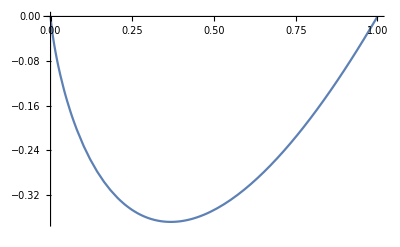

```mathematica
Plot[ r Log[r], {r, 0, 1}]
```